$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

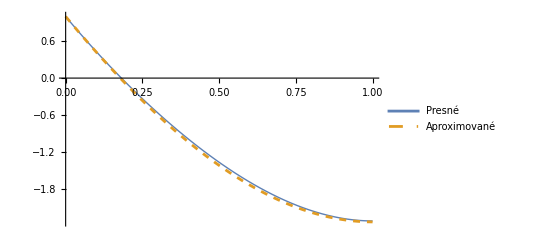

{0.0348207}

```mathematica
sol=DSolve[{-(1+x) u''[x]-u'[x]==-18 x^2,u[0]==1,u'[1]==0},u,x] ;(*Presné riešenie*)
U1[x_]:=1+2*(Power[x,2]−2x)+(2/3)*(Power[x, 3]−3x)
R1[x_]:=-((1+x) D[U1[x],x])+18 x^2;
n=2; 
phi[x_,i_]:=x^(i-1);
c=Table[c[i],{i,1,n}];
integrals1=Table[Integrate[R1[x]*phi[x,i],{x,0,1}]==0,{i,1,n}];
exactSolution[x_]:=u[x]/. sol;
Plot[{exactSolution[x],U1[x]},{x,0,1},PlotLegends->{"Presné","Aproximované"},PlotStyle->{Thick,Dashed}]
```

{{0.0348207}}

{{0.00234669}}

{{0.000265487}}

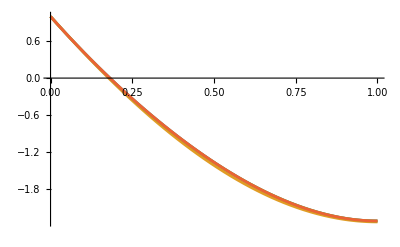

```mathematica
phi[x_,i_]:=x^(i-1);
fi[n_,x_]:=x^(n+1)-(n+1)*x;
U[n_,c_,x_]:=1+Sum[c[[i]]* fi[i,x],{i,1,n}]
U2[x_]:= U[2, {c1,c2}, x]
U3[x_]:= U[3, {c1,c2,c3}, x]
U4[x_]:= U[4, {c1,c2,c3,c4}, x]
R2[x_]:=-( D[(1+x)*U2'[x],x])+18 x^2
R3[x_]:=-( D[(1+x)*U3'[x],x])+18 x^2
R4[x_]:=-( D[(1+x) *U4'[x],x])+18 x^2
n=2;
integrals2=Table[Integrate[R2[x]*phi[x,i],{x,0,1}]==0,{i,1,n}];
n=3;
integrals3=Table[Integrate[R3[x]*phi[x,i],{x,0,1}]==0,{i,1,n}];
n=4;
integrals4=Table[Integrate[R4[x]*phi[x,i],{x,0,1}]==0,{i,1,n}];
koef2= Solve[integrals2, {c1,c2}];
koef3= Solve[integrals3, {c1,c2, c3}];
koef4= Solve[integrals4, {c1,c2,c3, c4}];
L2Error2=Sqrt[Integrate[(U2[x]-exactSolution[x])^2,{x,0,1}]] /.koef2//N
L2Error3=Sqrt[Integrate[(U3[x]-exactSolution[x])^2,{x,0,1}]] /.koef3//N
L2Error4=Sqrt[Integrate[(U4[x]-exactSolution[x])^2,{x,0,1}]]  /.koef4 //N
Plot[{exactSolution[x], U2[x]/.koef2, U3[x]/.koef3, U4[x]/.koef4}, {x,0,1}]
```

```mathematica
,
```